```mathematica
curr1=Import[NotebookDirectory[]<>"new.csv"];
curr2=Import[NotebookDirectory[]<>"new.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data={curr1[[All,5]],curr2[[All,2]]}//Transpose;
labels=curr1[[All,1]];
ListPlot[data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●},PlotLabel->"GAS",AxesLabel->{"ELECT","ETH"}]
```

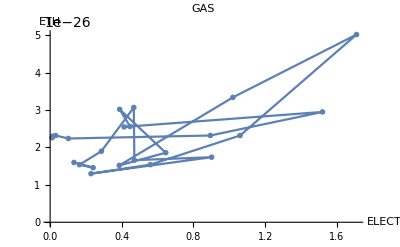
```mathematica
a=-Graphics-
```

```mathematica
a=-Graphics-
```

-Graphics-

```mathematica
a=-Graphics-
```

```mathematica
Export[NotebookDirectory[]<>"gaselectricityether.pdf",a,"PDF"]
```

/Users/Mahsa/Desktop/plots_new/New_ELECT_data/gaselectricityether.pdf

/Users/Mahsa/Desktop/plots_new/gaselectricityether.pdf

/Users/Mahsa/Desktop/plots_new/gaselectricityether.pdf

```mathematica
curr1=Import[NotebookDirectory[]<>"new.csv"];
curr2=Import[NotebookDirectory[]<>"new.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data={curr1[[All,3]],curr2[[All,2]]}//Transpose;
labels=curr1[[All,1]];
ListPlot[data ,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●},PlotLabel->"GAS",AxesLabel->{"USD","ETH"}]
```

```mathematica
a=-Graphics-
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"gasetherusd.pdf",a,"PDF"]
```

/Users/Mahsa/Desktop/plots_new/New_ELECT_data/gasetherusd.pdf